# Projektövning 2 - problemlösning i Mathematica

(Rapportskalet använder sig av ett stylesheet tillverkat av Göran Andersson)

Evan Saboo, Stefan Sarkis

## 1. Introduktion: problemformulering

Inom matematikkursen har vi fått i uppgift att lösa två olika matematiska problem med hjälp av Mathematica och dess programmeringsspråk. Syftet med detta introduktionsprojekt är att öva matematisk modellering, Mathematica och rapportskrivning.

Dessa två olika uppgifter handlar om att kunna skapa och modellera upp funktioner; skapa integraler och modellera upp dem;  använda olika metoder för att integrera olika funktioner t.ex. substitionsmetoden för hand; lösa ut differentialekvtion både med och utan Mathematica; och sist men inte minst kunna tolka graferna och dess resultat.

Målen med projektuppgifterna är att de ska underlätta inlärningen av kursinnehållet, de ska träna matematiskt modellbyggande samt att de ska ge träning i att tillverka och presentera rapporter.

### 1.1 Sammanfattning av uppgifter

#### 3.1

Denna uppgift gick ut på att man skulle definiera funktionen f(x)=√(p x^2+x^4),x∈ℝ, där p är ett tal mellan 1 och 31, och även modellera upp den i ett lämpligt intervall. Därefter bestämde vi∫_-1^2 f(x) dx och räknade ut arean både exakt och numeriskt. Sedan bestämde vi den primitiva funktionen F(x) och modellerade upp den i ett intervall på [-1, 2], samt beräknade höger respektive vänster gränsvärde för den problematiska punkten. För att räkna ut integralen för ett visst område använde vi oss av Integrate, vilket är den datatyp som är definerad för att lösa integralberäkningar i Mathematica. Efter det räknade vi ut integralen genom att dela upp hela integralen i två delar, och även för hand. Genom att dela upp den i två delar fick vi ett annorlunda svar vilket inte är beräknad som hela arean, men endast som två rektanglar inom det givna området. När vi räknade för hand med hjälp av substitutionsmetoden fick vi det rätta svaret till integralen som är ungefär lika med 11.6414 areaenheter.

#### 3.2

a)
I första deluppgiften ska man lösa ut och plotta differentialekvationen c’(t) = t^2 c^3 med begynnelsevillkoret  c(1) = p, där p är ett tal mellan 1 och 31. Sedan ska man få ut alla värden på t i lösningen. 
För att lösa deluppgiften använde vi  först datatypen DSolve för att lösa ut differentialekvationen med begynnelsevillkoret och plottade lösningen i en lämplig intervall. Sedan tog vi en del av lösningen och använde oss av Solve för att lösa ut alla värden på t i lösningsgrenen.

b) 
I den andra deluppgiften ska man lösa ut samma differentialekvation med samma begynnelsevillkor utan Mathematica (alltså för hand) och sedan ska man kontrollera om lösningen är korrekt.
Eftersom ekvationen är separabel så kunde vi lösa ut lösningrenen utan större problem och vi kontrollerade att lösningen stämmde med Mathematicas lösning.

c)
I den sista deluppgiften ska man formulera ett nytt randvillkor så att man får den andra lösningsgrenen i differantialekvationen  c’(t) = t^2 c^3 och sedan ska man få ut alla t i lösningsgrenen efter att man har plottat den.
Vi använde oss igen av DSolve utan något begynnelsevillkor för att få ut lösningsgrenarna i differntialekvationen. Vi formulerade sedan ut ett nytt begynnelsevillkor och använde DSolve för att bara få ut den andra lösningsgrenen och plottade den i en lämplig intervall.
till sist gorde samma sak som i den första delfrågan för att lösa ut alla värden på t.

## 2 Genomförande och härledningar

### 2.1 Uppgift 3.1)

#### a)

Hela uppgiften börjar med att man fick i uppdrag att modellera upp funktionen f(x)=√(p x^2+x^4) i ett lämpligt intervall, där p är ett eget val av tal mellan 1 och 31. Vi valde att tilldela p värdet 20 för denna uppgift, samt använda oss av intervallet [-31, 31] i x

```mathematica
p:= 20
```

```mathematica
f[x_]:=Sqrt[(p*x^2)+x^4]
```

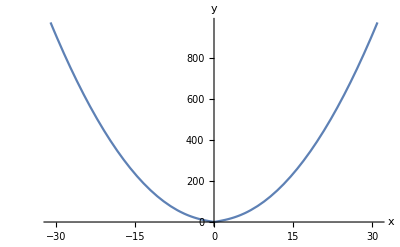

```mathematica
Plot[f[x],{x,-31,31},AxesLabel->{x,y}]
```

#### b)

Efter att ha modellerat upp funktionen inom ett lämpligt intervall var det dags att beräkna ut integralen av funktionen mellan gränsvärderna -1 och 2, d.v.s. ∫_-1^2 f(x) dx, både numeriskt och exakt.

```mathematica
x1:=-1
```

```mathematica
x2:=2
```

```mathematica
exakt:=Integrate[f[x],{x,x1,x2}]
```

```mathematica
exakt
```

-(80 √5)/3+16 √6+7 √21

```mathematica
numeriskt:=NIntegrate[f[x],{x,x1,x2}]
```

```mathematica
numeriskt
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

11.6414

```mathematica
exakt-numeriskt
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

1.35978×10^-7

#### c)

Nästa steg var att bestämma en primitiv funktion F(x) och modellera upp den över intervallet [-1, 2].

```mathematica
F[x_]=Integrate[f[x],x]
```

((x^2 (20+x^2))^(3/2))/(3 x^3)

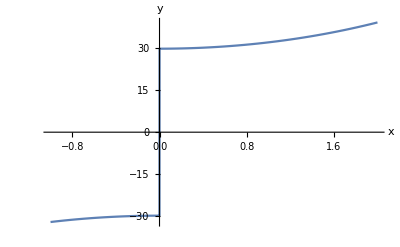

```mathematica
Plot[F[x],{x,x1,x2},AxesLabel->{x,y}]
```

Höger gränsvärde:

```mathematica
lim1:=Limit[F[x],x->0,Direction->-1]
```

```mathematica
lim1
```

(40 √5)/3

Vänster gränsvärde:

```mathematica
lim2 :=Limit[F[x],x->0,Direction->1]
```

```mathematica
lim2
```

-(40 √5)/3

#### d)

I denna deluppgift skulle man beräkna integralen med hjälp av huvudsatsen som lyder:∫_-1^2 f(x) dx=F(2)-F(-1); samt förklara vad det finns för fel och vilket det korrekta värdet är. Detta kommer tas upp i sista delen av rapporten - resultat, diskussion och slutsats.

```mathematica
F[x2]-F[x1]
```

16 √6+7 √21

#### e)

Här skulle man skriva om integralen ∫_-1^2 f(x) dx i två delar så att huvudsatsen kan användas. Vi valde att dela upp integralen i två delar.

```mathematica
Integrate[f[x],{x,-1,1}]+Integrate[f[x],{x,1,2}]
```

-(80 √5)/3+16 √6+7 √21

```mathematica
x3:=1
```

```mathematica
(F[x3]-F[x1])+(F[x2]-F[x3])+ lim2-lim1
```

-(80 √5)/3+16 √6+7 √21

#### f)

I den sista deluppgiften skulle man beräkna integralen för ∫_-1^2 f(x) dx genom att använda sig av substitutionsmetoden för att lösa uppgiften.

-Graphics-

### 2.2 Uppgift 3.2)

#### a)

Först rensar vi alla globala variablar från dess värden, sedan använder vi dataypen DSolve för att lösa ut  differentialekvationen c’(t) = t^2 c^3 med begynnesevillkortet  c(1) = p där vi har definierat p som 20 för att begynnelsevillkoret ska gälla.

```mathematica
ClearAll["`*"]
```

```mathematica
p :=20
```

```mathematica
sol=DSolve[{ c'[t]==t^2*c[t]^3,c[1]==p},c[t], t]
```

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

{{c[t]→(20 √3)/(√(803-800 t^3))}}

Efter att vi fick ut lösningen plottar vi det i en lämplig intervall och markerar begynnelsevillkortet p(1)=20.

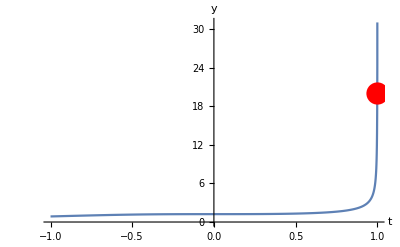

```mathematica
Plot[c[t]/.sol,{t,-1,2},AxesLabel->{t,y},PlotRange->{0,31},Epilog->{PointSize[.04], Red,Point[{1,p}]}]
```

I sista delen av uppgiften använder vi datatypen Solve för att lösa ut alla t vår lösning gäller för.

```mathematica
Solve[Sqrt[803-800 t^3]==0]
```

{{t→-(-803)^(1/3)/(2 10^(2/3))},{t→803^(1/3)/(2 10^(2/3))},{t→((-1)^(2/3) 803^(1/3))/(2 10^(2/3))}}

Vi fick ut tre olika t som vår lösning gäller för.

#### b)

I den andra deluppgiften löser vi ut differentialekvationen för hand. Eftersom vi vet att ekvationen är en separabel differentialekvation så kan vi lösa det utan någon större problem.
-Graphics-

Efter att vi fick ut lösningen med hand plottar vi det i ett lämpligt intervall.

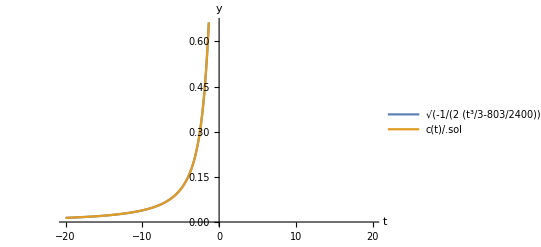

```mathematica
Plot[{Sqrt[-(1/2)/(((t^3)/3)-(803/2400))],c[t]/.sol},{t,-20,20},AxesLabel-> {t,y},  PlotLegends->"Expressions"]
```

Vi plottar också ut Mathematicas lösning i samma graf för att kunna jämföra det med den handskrivna lösningen.

#### c)

I sista deluppgiften ska vi plotta ut den andra lösningsgrenen till differentialekvationen c’(t) = t^2 c^3. Första löser vi ut båda lösningsgrenarna på ekvationen genom att använda datatypen DSolve utan att ha med begynnelsevillkoret p(0)=20 . Om vi har med begynnelsevillkoret kommer bara en lösningsgren att skrivas ut.

```mathematica
ClearAll["`*"]
```

```mathematica
sol=DSolve[ c'[t]==t^2*c[t]^3,c[t], t]
```

{{c[t]→-(√(3/2))/(√(-t^3-3 C[1]))},{c[t]→(√(3/2))/(√(-t^3-3 C[1]))}}

Här ser vi att den andra lösningsgrenen är en negativ ekvation. Genom att sätta begynnelsevillkortet p som -20 så kan vi få ut den odefinerade konstanten C[1] i den negativa lösningensgrenen genom DSolve. Vi plottar sedan ut den negativa lösningen i intervallet [-1,2].

```mathematica
p:=-20;
```

```mathematica
sol=DSolve[{ c'[t]==t^2*c[t]^3,c[1]==p},c[t], t]
```

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

{{c[t]→-(20 √3)/(√(803-800 t^3))}}

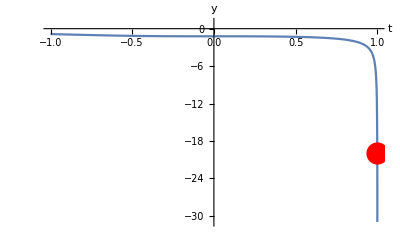

```mathematica
Plot[c[t]/.sol, {t, -1,2}, AxesLabel->{t,y}, PlotRange->{-31,1},Epilog->{PointSize[.04], Red,Point[{1,p}]}]
```

Som i första delfrågan använder vi Solve för att få ut alla t i den negativa lösningen.

```mathematica
Solve[(-Sqrt[803-800 t^3])==0]
```

{{t→-(-803)^(1/3)/(2 10^(2/3))},{t→803^(1/3)/(2 10^(2/3))},{t→((-1)^(2/3) 803^(1/3))/(2 10^(2/3))}}

## 3. Resultat, diskussion och slutsats

### Uppgift 3.1

Här visar en tabell på vissa resultat vi fick under uppgiftets genomgång. 
f(x) | F(x) | H. gränsvärde | V. gränsvärde
√(20 x^2+x^4) | ((x^2 (20+x^2))^(3/2))/(3 x^3) | (40 √5)/3 | -(40 √5)/3
Beräkningen av integralen i den andra deluppgiften gav oss resultatet att arean i det givna intervallet; [-1, 2]; är lika med (-(80 √5)/3+16 √6+7 √21) areaenheter och det är ungefär lika med 11.6414 areaenheter om man avrundar det till ett godtyckligt tal. Vi valde att jämföra dessa två resultat med varandra genom att subtrahera den numeriska integralen från den exakta integralen, och därmed fick vi att differensen är 1.35978×10^-7 a.e. Därmed ser vi att den exakta lösningen är väldigt lite större än den numeriska lösningen.
När vi däremot delade upp integralen och beräknade den med hjälp av huvudsatsen, dvs ∫_-1^2 f(x) dx=F(2)-F(-1), fick vi ett litet annorlunda svar. Då blev svaret 16 √6+7 √21 areaenheter. Vi ser att hela (-(80 √5)/3)-termen har försvunnit ur svaret. Huvudsatsen räknar ut hela integralen utan att ta hänsyn till den problematiska lnjen mellan gränsvärderna i funktionen. Genom att subtrahera skillnaden mellan de negativa och positiva gränsvärderna så får vi den korrekta lösningen för funktionen.
Vi beräknade även integralen för hand med hjälp av substitutionsmetoden och fick fram att resultatet är  [7 √21-(20 √20)/3]+[8 √24-(20 √20)/3] areaenheter, vilket är ungefär lika med 11.6414 areaenheter.
Därmed har vi beräknat integralen med hjälp av Mathematica samt för hand och fått likadana slutresultat.

### Uppgift 3.2

#### a)

I första deluppgiften fick vi en lösningsgren på differentialekvationen c’(t) = t^2 c^3 med begynnesevillkortet  c(1) = 20 med hjälp av datatypen DSolve. Lösningen är:(20 √3)/(√(803-800 t^3)).
-Graphics-

Grafen visar lösningen till differentialekvationen med det markerade begynnelsevillkoret c(1) = 20, där t=1 och y = 20.

För att få ut vilka t vår lösning gäller så använde vi datatypen Solve och fick ut tre t eftersom lösnnigen är en tredjegradsekvation:

{{t→-(-803)^(1/3)/(2 10^(2/3))},{t→803^(1/3)/(2 10^(2/3))},{t→((-1)^(2/3) 803^(1/3))/(2 10^(2/3))}}

#### b)

Vi löste ut differentialekvationen c’(t) = t^2 c^3 med begynnesevillkoret  c(1) = 20 för hand och fick lösningen: Sqrt[-0.5/(((t^3)/3)].
Vi kan bevisa att lösningen stämmer med Mathematicas lösning genom 2 metoder.

1. Den första metoden går ut på att plotta den handskrivna lösningsgrenen tillsammans med  Mathematicas lösningsgren för att de ska synnas i samma graf.
-Graphics-

Vi kan se i grafen att linjerna är identiska med varandra och då kan komma fram till att lösningsgrenarna är likadana. I grafen ser man inte den blåa linjen men detta beror på att funktionerna är identiska med varandra.

2. I den andra metoden ska vi pröva att sätta in t=1 i den handrskrivna lösningen.

```mathematica
ClearAll["`*"]
```

```mathematica
c[t_]=Sqrt[-(1/2)/(((t^3)/3)-(803/2400))]
```

(√(-1/(-803/2400+t^3/3)))/(√2)

```mathematica
c[1]
```

20

Svaret 20 som stämmer med begynnelsevillkortet p(1)=20. och vi kan komma fram till att ekvationen (lösningrenen) är korrekt.

#### c)

I den sista deluppgiften ska vi få ut den andra lösningsgrenen genom att först använda dataypen DSolve för att lösa ut diffentialekvationen  c’(t) = t^2 c^3 utan randvillkort.
Vi får ut dessa lösningar: {{c[t]→-(√(3/2))/(√(-t^3-3 C[1]))},{c[t]→(√(3/2))/(√(-t^3-3 C[1]))}}.
Vi ser att den andra lösningsgrenen är negativ så vi använder DSolve och begynnelsevillkoret p(1)=-20  för att bara få ut den negativa lösningsgrenen.
 -Graphics-
Här har vi plottat ut den andra lösningsgrenen i ett lämpligt intervall med begynellsevillkortet (1) = -20.

För att få ut vilka t vår andra lösningsgren gäller så använde vi datatypen Solve och fick ut tre t eftersom lösningsgrenen är en tredjegradspolynom:

{{t→-(-803)^(1/3)/(2 10^(2/3))},{t→803^(1/3)/(2 10^(2/3))},{t→((-1)^(2/3) 803^(1/3))/(2 10^(2/3))}}

Vi ser att alla t i den negativa lösningsgrenen är identiska med den positiva lösningsgrenens  t.